## Pre-Computing the BRDF Integral

We need to find a way to approximate the lighting integral for the specular part of our area light.
The integral writes as:

	L(ω_o)=∫_Ω L(ω_i) f_r(ω_o,ω_i)(ω_i.n)dω_i
	
Ω is the solid angle covered by the upper hemisphere above the surface.

We proceed in the same way as http://blog.selfshadow.com/publications/s2013-shading-course/karis/s2013_pbs_epic _notes _v2.pdf to separate the integral in several parts:

#### Splitting the integral

L(ω_o)≃ ∫_Ω L(ω_i,ρ) (ω_i.n) dω_i  ∫_Ω f_r(ω_o,ω_i)(ω_i.n)dω_i

∫_Ω L'(ω_i,ρ) (ω_i.n) dω_i  represents the pre-filtered source of radiance. It could be an env-map in the case of IBL, or our area light in this case.
∫_Ω f_r(ω_o,ω_i)(ω_i.n)dω_i represents the BRDF integral as if lit by a uniform source of radiance (L(ω_i)=1).

#### BRDF integral

Here, we’ re going to concentrate on the BRDF integral.
Assuming the BRDF f_r(ω_o,ω_i) is our Ward-Dür model, coupled with Fresnel, we obtain:

	L_brdf(ω_o)≃ ∫_Ω  F(ω_o,ω_i,n) D(ω_o,ω_i,n) (ω_i.n)dω_i

F(ω_o,ω_i,n) is the Fresnel term (note that we’ll use the Schlick' s fresnel approximation, not our complex fresnel otherwise the integral would be more difficult to separate).
D(ω_o,ω_i,n) is the Normal Distribution Function of the micro-facet model.
There is no masking/shadowing term as it is already accounted for by the Ward-Dür NDF.

Assuming the Schlick fresnel term is:

	F_schlick(ω_o,h)=F_0+(1-F_0)(1-ω_o.h)^5 = F_0 (1-(1-ω_o.h)^5) + (1-ω_o.h)^5 

We can further split the integral into 2 parts:

	L_brdf(ω_o)≃ F_0∫_Ω  (1-(1-ω_o.h)^5)D(ω_o,ω_i,n) (ω_i.n)dω_i + ∫_Ω  (1-ω_o.h)^5 D(ω_o,ω_i,n) (ω_i.n)dω_i

Ignoring anisotropy, we have:

	D(ω_o,ω_i,n,α) = ρ_s/πα^2 e^(-(tan^2 Θ_h)/α^2) 2(1+cos Θ_l cos Θ_v +sin Θ_l sin Θ_v cos( Φ_v-Φ_l))/(cos Θ_l + cos Θ_v)^4 

Or:
	D(ω_o,ω_i,n,α) = ρ_s/πα^2 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4
	
and ĥ = ω_o +ω_i  (non-normalized!)
	
This gives us:

	L_brdf(ω_o,α)≃ ρ_s/πα^2[ F_0∫_Ω  (1-(1-ω_o.h)^5)e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 (ω_i.n)dω_i + ∫_Ω  (1-ω_o.h)^5 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 (ω_i.n)dω_i]
	
	L_brdf(ω_o.n,α)≃ ρ_s/2[F_0 A(ω_o.n,α) +B(ω_o.n,α)]

Where:
	A(ω_o.n,α)= 1/α^2∫_0^(π/2)  (1-(1-ω_o.n)^5)e^(-(tan^2 Θ_h)/α^2)(ĥ.ĥ)/(ĥ.n)^4 sin Θ dΘ
	B(ω_o.n,α) = 1/α^2∫_0^(π/2)  (1-ω_o.n)^5 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 sin Θ dΘ

Both A and B are bounded in [0,1] because the integral of BRDF is ≤ 1, as shown by Dür in his paper.

#### WRONG! Light direction is NOT the reflected view direction! Now, in our special case, we also have the incoming (light) direction ω_i which is the reflection of the outgoing (view) direction: ω_i= 2(ω_o.n).n - ω_o or simply, in terms of angles, Θ_l=Θ_v and Φ_l=Φ_v+π h = (ω_i+ω_o)/(|ω_i+ω_o|)=(2(ω_o.n).n)/(2(ω_o.n))=n So D(ω_o,ω_i,n) further simplifies into: D(ω_o,ω_i,n) = ρ_s/πα^2 e^(-((tan Θ_h)/α^2)^2) 2(1+cos Θ_l cos Θ_v +sin Θ_l sin Θ_v cos( Φ_v-Φ_l))/(cos Θ_l + cos Θ_v)^4 = ρ_s/πα^2 2(1+cos^2 Θ_v -sin^2 Θ_v )/(2 cos Θ_v)^4=ρ_s/πα^2(4 cos^2 Θ_v)/(16 cos^4 Θ_v)=ρ_s/(4 πα^2 cos^2 Θ_v) And L_brdf(ω_o) becomes: L_brdf(ω_o.n,α)≃ ρ_s/(4π)[F_0∫_Ω (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))dω_i +∫_Ω (1-ω_o.n)^5 1/(α^2(ω_o.n))dω_i] L_brdf(ω_o.n,α)≃ ρ_s/2[F_0∫_0^(π/2) (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))sin Θ dΘ +∫_0^(π/2) (1-ω_o.n)^5 1/(α^2(ω_o.n))sin Θ dΘ] L_brdf(ω_o.n,α)≃ ρ_s/2[F_0 A(ω_o.n,α) +B(ω_o.n,α)] Where: A(ω_o.n,α)= ∫_0^(π/2) (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))sin Θ dΘ B(ω_o.n,α) = ∫_0^(π/2) (1-ω_o.n)^5 1/(α^2(ω_o.n))sin Θ dΘ

### Plotting the 2 parts

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]; 
rawBRDFpart = BinaryReadList["./BRDF0_64x64.bin",{"Real32", "Real32"}]
```

{{0.00031613,0.997731},{0.0757202,0.924233},{0.146784,0.853202},{0.213407,0.786586},{0.275802,0.724193},{0.334173,0.665822},{0.388719,0.611279},{0.43963,0.560368},4080,{0.497822,0.000302614},{0.495718,0.000243381},{0.493593,0.000192446},{0.491529,0.000150126},{0.489565,0.000114701},{0.48753,0.0000850902},{0.485661,0.0000613634},{0.483746,0.0000416179}}
 |  |  |  |

```mathematica
BRDFpartA = Table[{Mod[i,64]/63,Quotient[i,64]/63,rawBRDFpart[[1+i]][[1]]}, {i,0,64*64-1}];
BRDFpartB = Table[{Mod[i,64]/63,Quotient[i,64]/63,rawBRDFpart[[1+i]][[2]]}, {i,0,64*64-1}];
ListPlot3D[BRDFpartA,AxesLabel->{"N.V cos(θ)","Roughness"}]
ListPlot3D[BRDFpartB,PlotRange->Full,AxesLabel->{"N.V cos(θ)","Roughness"}]
```

-Graphics3D-

-Graphics3D-

```mathematica
BRDFpartA[[1+64*63+63]]
```

{1,1,0.483746}

### Finding an analytical estimate for these curves

Now that we know the aspect of these curves, maybe we can find a nice fit with traditional polynomials or exponential functions?

#### Let’s try and fit the F0-independant curve (part B)

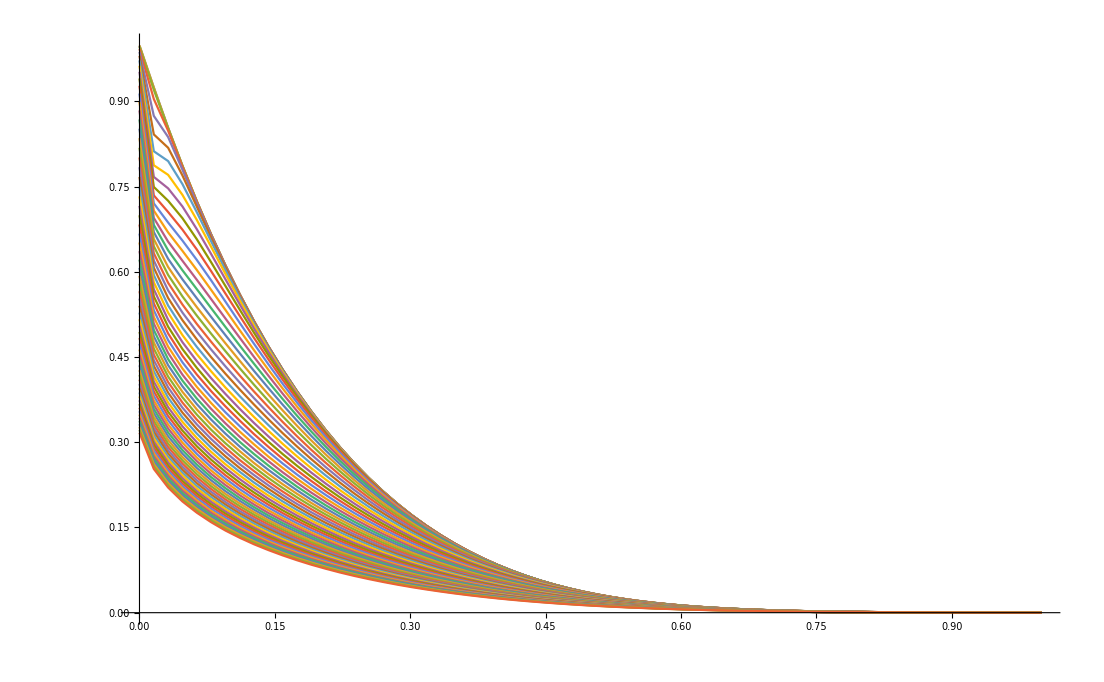

```mathematica
curvesB=Table[Table[{(NdV-1)/63,rawBRDFpart[[1+64*(Roughness-1)+(NdV-1)]][[2]]},{NdV,1,64}],{Roughness,1,64,1}];
ListLinePlot[curvesB,PlotRange->All]
```

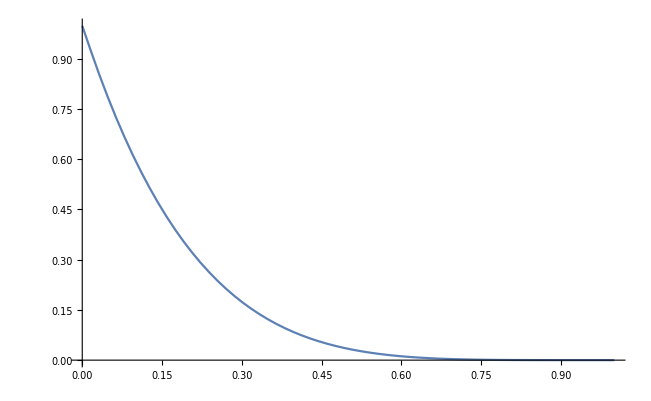

```mathematica
ListLinePlot[curvesB[[1]],PlotRange->All]
```

{a→0.987192,b→-4.71456,c→8.59749,d→-7.06676,e→2.19865}

Function[x,0.987192-4.71456 x+8.59749 x^2-7.06676 x^3+2.19865 x^4]

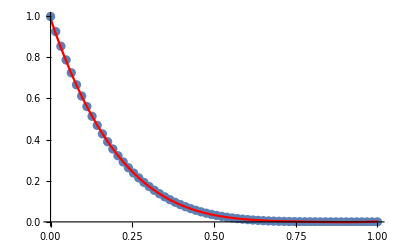

```mathematica
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";



(*modelOriginB=Exp[-a*Sin[c*x]^b];*)
modelB=a+b*x+c*x^2;
modelB=a+b*x+c*x^2+d*x^3;
modelB=a*Exp[b*x^c];
modelB=a+b*x+c*x^2+d*x^3+e*x^4;
fittingB = FindFit[curvesB[[4]],modelB,{a,b,c,d,e},x,Method->fittingMethod]
functionB =Function[x,Evaluate[ modelB/.fittingB]]
Show[
ListPlot[curvesB[[1]]],
Plot[functionB[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

```mathematica
curvesB[[1]][[1]][[2]]
```

0.997731

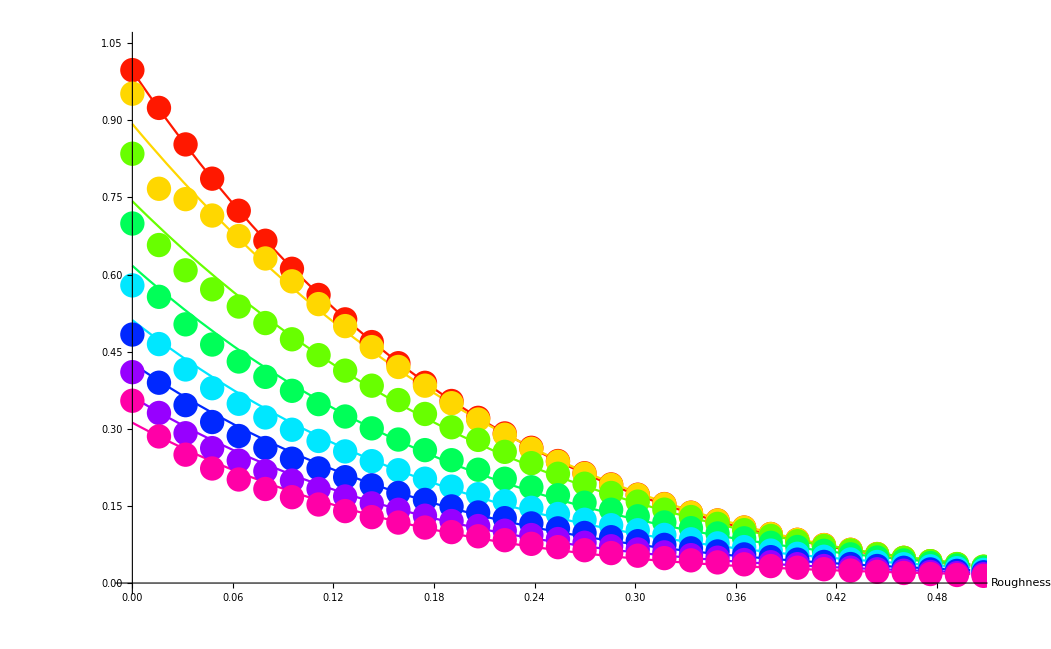

```mathematica
(*fittingB = Table[FindFit[ curvesB[[j]],modelOriginB/.a-> curvesB[[j]][[1]][[2]],{b},x ],{j,1,64}];*)
fittingB = Table[FindFit[ curvesB[[j]],modelB,{a,b,c,d,e},x ,Method->fittingMethod],{j,1,64}];
MatrixForm[fittingB];
MatrixForm[modelB/.fittingB];

Show[
Table[Plot[modelB/.fittingB[[j]],{x,0,0.5},PlotRange->{0,1.05},PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64,8}],
Table[ListPlot[curvesB[[j]],PlotRange->{0,0.5} ,PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64,8}]
]
```

### Representing & Fitting Individual Parameters

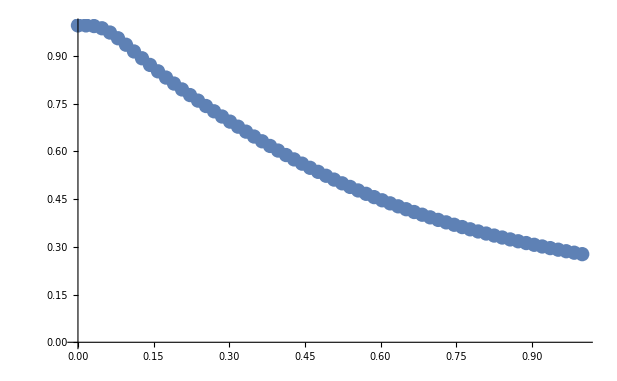

```mathematica
curvesBa = Table[{(i-1)/63, a/.fittingB[[i]]},{i,1,64}];
curvesBb = Table[{(i-1)/63, b/.fittingB[[i]]},{i,1,64}];curvesBc = Table[{(i-1)/63, c/.fittingB[[i]]},{i,1,64}];curvesBd = Table[{(i-1)/63, d/.fittingB[[i]]},{i,1,64}];
curvesBe = Table[{(i-1)/63, e/.fittingB[[i]]},{i,1,64}];(*curvesBf = Table[{(i-1)/63, f/.fittingCurvesB[[i]]},{i,1,64}];ListPlot[{curvesBa,curvesBb,curvesBc,curvesBd,curvesBe,curvesBf}]*)
ListPlot[curvesBa]
ListPlot[{curvesBa,curvesBb,curvesBc,curvesBd,curvesBe}];
```

#### Now fitting a,b,c,d,e

Now that we know the behavior of coefficients a, b, c, d & e depending on roughness, we can try and fit them too!

```mathematica
fittingMethod="Automatic";
(*fittingMethod="PrincipalAxis";*)
(*fittingMethod="InteriorPoint";*)
(*fittingMethod="Newton";*)
(*fittingMethod="QuasiNewton";*)
(*fittingMethod="LevenbergMarquardt";*)
(*fittingMethod="ConjugateGradient";*)

generalModelCoeffs = a+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
generalModelCoeffs = a+b*x+c*x^2;
(*generalModelCoeffs = a+b*x+c*Exp[d*x]*Cos[e*x];*)

(* Use modelOriginB function for our initial parameter a *)
(*generalModelCoeffs = Evaluate[modelOriginB[x]]+b*x+c*x^2+d*x^3+e*x^4+f*x^5*)
```

Function[x,1.0404-1.31701 x+0.557022 x^2]

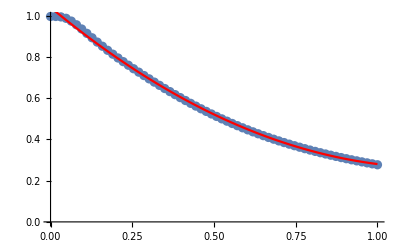

```mathematica
modelCoeffA=generalModelCoeffs;
fittingCoeffA = FindFit[curvesBa,modelCoeffA,{{a,-5},{b,2},{c,0.1},{d,-1},e,f},x,Method->fittingMethod];
modelCoeffA = Function[x,Evaluate[modelCoeffA/.fittingCoeffA]]
Show[
ListPlot[curvesBa],
Plot[modelCoeffA[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

#### Test

We know that modelB=a+b*x+c*x^2+d*x^3+e*x^4 
And a

```mathematica
Function[x,1.040396538714005-1.3170092599380083 x+0.5570217759489628 x^2]
```

Function[x,1.0404-1.31701 x+0.557022 x^2]

Function[x,-4.69724+5.75169 x-2.77787 x^2]

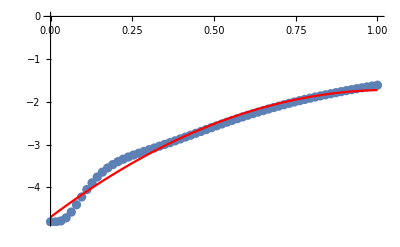

```mathematica
modelCoeffB=generalModelCoeffs;
fittingCoeffB = FindFit[curvesBb,modelCoeffB,{{a,11},{b,0},{c,10},{d,-0.1},{e,4},f},x,Method->fittingMethod];
modelCoeffB = Function[x,Evaluate[modelCoeffB/.fittingCoeffB]]
Show[
ListPlot[curvesBb],
Plot[modelCoeffB[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

Function[x,7.85-7.73803 x+4.05125 x^2]

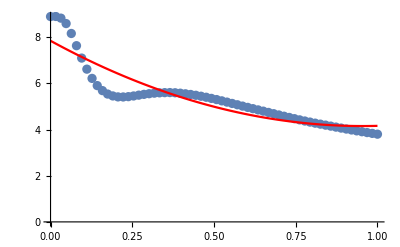

```mathematica
modelCoeffC=generalModelCoeffs;
fittingCoeffC = FindFit[curvesBc,modelCoeffC,{{a,-18},{b,0},{c,10},{d,-1.0},{e,2},f},x,Method->fittingMethod];
modelCoeffC = Function[x,Evaluate[modelCoeffC/.fittingCoeffC]]
Show[
ListPlot[curvesBc],
Plot[modelCoeffC[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

Function[x,-5.72904+2.84643 x-1.57185 x^2]

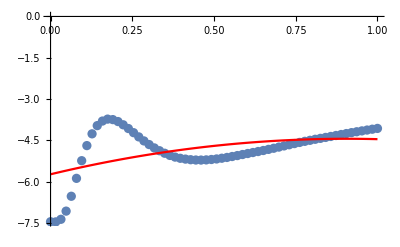

```mathematica
modelCoeffD=generalModelCoeffs;
fittingCoeffD = FindFit[curvesBd,modelCoeffD,{{a,18},{b,0},{c,-10},{d,-1},{e,3},f},x,Method->fittingMethod];
modelCoeffD = Function[x,Evaluate[modelCoeffD/.fittingCoeffD]]
Show[
ListPlot[curvesBd],
Plot[modelCoeffD[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

Function[x,1.53352+0.487724 x-0.279866 x^2]

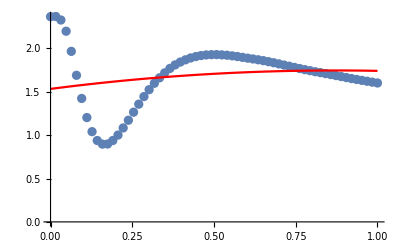

```mathematica
modelCoeffE=generalModelCoeffs;
fittingCoeffE = FindFit[curvesBe,modelCoeffE,{{a,-5},{b,-0.5},{c,5},{d,-1},{e,3},f},x,Method->fittingMethod];
modelCoeffE = Function[x,Evaluate[modelCoeffE/.fittingCoeffE]]
Show[
ListPlot[curvesBe],
Plot[modelCoeffE[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

### Plotting the result & comparing with data

```mathematica
(*fitB[NdotV_,r_]:=modelCoeffA[r]+modelCoeffB[r]*NdotV+modelCoeffC[r]*NdotV^2+modelCoeffD[r]*NdotV^3;*)
(*fitB[NdotV_,r_]:=modelCoeffA[r]+modelCoeffB[r]*NdotV+modelCoeffC[r]*NdotV^2+modelCoeffD[r]*NdotV^3+modelCoeffE[r]*NdotV^4;*)

fitB[NdotV_,r_]:=modelCoeffA[r]*NdotV+modelCoeffB[r]*NdotV^2+modelCoeffC[r]*NdotV^3+modelCoeffD[r]*NdotV^4+modelCoeffE[r]*NdotV^5;

Show[Plot3D[fitB[NdotV,r],{NdotV,0,1},{r,0,1},PlotRange->{0,1},AxesLabel->{"N.V","Roughness"},PlotStyle->ColorData["RedBlueTones"]],
ListPlot3D[BRDFpartB,PlotRange->Full,AxesLabel->{"N.V","Roughness"}]]
```

-Graphics3D-

#### Test directly fitting a 3D function...

```mathematica
(*data=Table[{(Mod[i,64])/63,Floor[i/64] / 63,BRDFpartB[[1+Floor[i/64]]][[1+Floor[Mod[i,64]]]]},{i,0,128,1}];*)
```

```mathematica
data=BRDFpartB;
Clear[a,b,c,d,f,g,h,i,j,k,l,m,n,o]
ListPlot3D[data,PlotRange->{{0,1},{0,1},{0,1}},AxesLabel->{"x","y"}]

fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

(*pipoModel =a+b*x+c*x^2 d*x^3+e*y+f*y^2+ g*x*y;*)
(*data=Table[{Mod[i,64]/63,Floor[i/64] / 63,BRDFpartB[[1+Floor[i/64]]][[1+Floor[Mod[i,64]]]]},{i,0,64*64-1,1}];*)

(* Exponential model
pipoModel =c*Exp[a*(x-x0)+b*(y-y0)];
pipoFit=FindFit[data,pipoModel,{{a,0},{b,1},{c,1},{d,1},e,{f,1},g,h,i,x0,y0,x1,y1},{x,y},Method->fittingMethod];
*)
(* Exp2 model *)
pipoModel =c*Power[2,a*(x-x0)+b*(y-y0)];

pipoModel =1+a*x+b*x^2+c*y +d*x*y+e*x^2*y+f*y^2+g*x*y^2+h*x^2*y^2;
pipoModel =1+a*x+b*x^2+c*x^3+d*y+e*x*y+ f*x^2*y+g*x^3*y+h*y^2+i*x*y^2+j*x^2*y^2+k*x^3*y^2+l*y^3+m*x*y^3+n*x^2*y^3+o*x^3*y^3;

pipoFit=FindFit[data,pipoModel,{{a,1},{b,1},{c,1},{d,1},e,{f,1},g,h,i,j, k, l, m,n,o},{x,y},Method->fittingMethod];
pipoModel=Function[{x,y},Evaluate[pipoModel/.pipoFit]]

Plot3D[pipoModel[x,y],{x,0,1},{y,0,1},PlotRange->{{0,1},{0,1},{0,1.05}},AxesLabel->{"x","y"}]
Show[ListPlot3D[data,PlotRange->Full],Plot3D[pipoModel[x,y],{x,0,1},{y,0,1},PlotRange->{-0.05,1.05},PlotStyle->Red]]
```

-Graphics3D-

Function[{x,y},1-4.26837 x+5.98938 x^2-2.74588 x^3-1.11698 y+6.24858 x y-10.3598 x^2 y+5.29659 x^3 y+0.0800559 y^2-4.05788 x y^2+10.0246 x^2 y^2-6.18378 x^3 y^2+0.307577 y^3+0.896599 x y^3-3.93271 x^2 y^3+2.81093 x^3 y^3]

-Graphics3D-

-Graphics3D-

```mathematica
1-4.268373376557555 x+5.9893822170455895 x^2-2.745876982205202 x^3-1.1169779635363377 y+6.2485832361009965 x y-10.359824418695426 x^2 y+5.296592577623529 x^3 y+0.08005589283505338 y^2-4.057878478465465 x y^2+10.024587584890986 x^2 y^2-6.183779761950312 x^3 y^2+0.3075771997708405 y^3+0.8965992421669212 x y^3-3.9327120832393003 x^2 y^3+2.8109277250321485 x^3 y^3
```

```mathematica
1-3.10644824089575 x+2.2442720252458033 x^2-1.5631045930597178 y+5.286682741799993 x y-4.013072795013668 x^2 y+0.8078765587702772 y^2-2.9710821881549427 x y^2+2.3561138954372183 x^2 y^2
```

```mathematica
errAbs=Table[{data[[i]][[1]],data[[i]][[2]],100.0*Abs[data[[i]][[3]]-pipoModel[Mod[i-1,64]/63,Quotient[i-1,64]/63]]},{i,1,64*64}];
errRel=Table[{data[[i]][[1]],data[[i]][[2]],100.0*Abs[data[[i]][[3]]/Max[0.0001,pipoModel[Mod[i-1,64]/63,Quotient[i-1,64]/63]]-1]},{i,1,64*64}];
ListPlot3D[errAbs,PlotRange->{0,100}]
ListPlot3D[errRel,PlotRange->{0,100}]
```

-Graphics3D-

-Graphics3D-

Fitting the F0-dependant curve

```mathematica
(*data=Table[{(Mod[i,64])/63,Floor[i/64] / 63,BRDFpartB[[1+Floor[i/64]]][[1+Floor[Mod[i,64]]]]},{i,0,128,1}];*)
```

```mathematica
data=BRDFpartA;
Clear[a,b,c,d,f,g,h,i,j,k,l,m,n,o]
(*ListPlot3D[data,PlotRange->{{0,1},{0,1},{0,1}},AxesLabel->{"x","y"}]*)

fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

pipoModel =a*x+b*x^2+c*y +d*x*y+e*x^2*y+f*y^2+g*x*y^2+h*x^2*y^2;
pipoModel =a*x+b*x^2+c*x^3+d*y+e*x*y+ f*x^2*y+g*x^3*y+h*y^2+i*x*y^2+j*x^2*y^2+k*x^3*y^2+l*y^3+m*x*y^3+n*x^2*y^3+o*x^3*y^3;

pipoFit=FindFit[data,pipoModel,{{a,1},{b,1},{c,1},{d,1},e,{f,1},g,h,i,j,k,l,m,n,o},{x,y},Method->fittingMethod];
pipoModel=Function[{x,y},Evaluate[pipoModel/.pipoFit]]

Plot3D[pipoModel[x,y],{x,0,1},{y,0,1},PlotRange->{{0,1},{0,1},{0,1.2}},AxesLabel->{"x","y"}]
Show[ListPlot3D[data,PlotRange->{0,1.5}],Plot3D[Min[1,pipoModel[x,y]],{x,0,1},{y,0,1},PlotStyle->Red]]
```

Function[{x,y},4.48312 x-6.60742 x^2+3.13691 x^3+0.319656 y-4.17156 x y+10.5793 x^2 y-6.40718 x^3 y+1.48122 y^2-5.67918 x y^2-0.173547 x^2 y^2+2.90601 x^3 y^2-1.14831 y^3+5.28977 x y^3-4.03338 x^2 y^3+0.496314 x^3 y^3]

-Graphics3D-

-Graphics3D-

```mathematica
4.483120094766527 x-6.607418162702069 x^2+3.1369146126741314 x^3+0.31965568814498413 y-4.171560969733041 x y+10.579256413997497 x^2 y-6.407181973132758 x^3 y+1.4812238752410947 y^2-5.679180293057831 x y^2-0.17354724317745246 x^2 y^2+2.9060079735435256 x^3 y^2-1.1483095194551398 y^3+5.289774653050149 x y^3-4.03337882134342 x^2 y^3+0.496313678299834 x^3 y^3
```

```mathematica
3.2341316749472577 x-2.373272450906272 x^2+1.0643192106211778 y-4.840084966583103 x y+4.174411960036787 x^2 y-0.38184478124695787 y^2+1.3304731349921781 x y^2-1.779774293647103 x^2 y^2
```

```mathematica
errAbs=Table[{data[[i]][[1]],data[[i]][[2]],100.0*Abs[data[[i]][[3]]-pipoModel[Mod[i-1,64]/63,Quotient[i-1,64]/63]]},{i,1,64*64}];
errRel=Table[{data[[i]][[1]],data[[i]][[2]],100.0*Abs[data[[i]][[3]]/pipoModel[Mod[i-1,64]/63,Quotient[i-1,64]/63]-1]},{i,1,64*64}];
ListPlot3D[errAbs,PlotRange->{0,100}]
ListPlot3D[errRel,PlotRange->{0,100}]
```

Power::infy: Infinite expression 1/0. encountered.

-Graphics3D-

-Graphics3D-

## Paraboloïd Shadow Mapping

```mathematica
Plot3D[{1-x^2-y^2,0},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

### Using a sigmoïd to simulate the step function

```mathematica
sigmoid[x_,k_] := 1 / (1+Exp[-k*x]);
Manipulate[Plot[sigmoid[x,k], {x,-10, 10},PlotRange->Full], {{k,1},1/100,100}]
```

```mathematica
Series[sigmoid[x,10],{x,0,8}]
```

1/2+(5 x)/2-(125 x^3)/6+(625 x^5)/3-(265625 x^7)/126+O[x]^9

```mathematica
approx[x_]:=1/2+(5 x)/2-(125 x^3)/6+(625 x^5)/3-(265625 x^7)/126
```

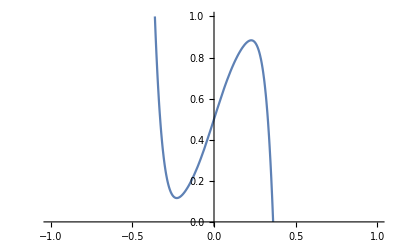

```mathematica
Plot[approx[x],{x,-1,1},PlotRange->{0,1}]
```

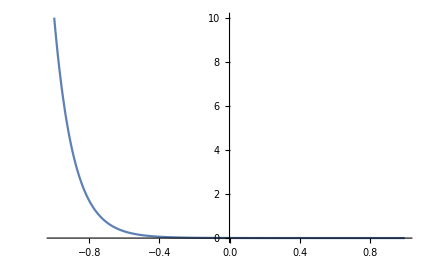

```mathematica
a = 1.0;
b =  0.1;
altitude = 100.0;
hitDistance = 100.0;
density[dy_]:= a  Exp[-b * altitude] (1 - Exp[-b * dy * hitDistance]) / (b * dy);
Plot[density[x], {x, -1.0, 1 }, PlotRange->Full]
```